```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/66436371.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
trX1X2 = Table[{cmatdata[[A, 1]], Tr[cmatdata[[A, 2]].cmatdata[[A, 3]]]//Chop}, {A, 1, Length[cmatdata]}];
```

```mathematica
trX5X9 = Table[{cmatdata[[A, 1]], Tr[cmatdata[[A, 6]].cmatdata[[A, 10]]]//Chop}, {A, 1, Length[cmatdata]}];
```

```mathematica
trX1sq = Table[{cmatdata[[A, 1]], (Tr[cmatdata[[A, 2]].cmatdata[[A, 2]]]-1/($K)Sum[Tr[cmatdata[[A, i]].cmatdata[[A, i]]], {i, 2, $K+1}])//Chop}, {A, 1, Length[cmatdata]}];
```

```mathematica
fig = ListPlot[{trX1X2, trX5X9, trX1sq},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"t", "\\mathcal{O}_i"},
FrameTicks->{{With[{ticks=-0.15+0.1Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=10Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotLegends->Placed[MaTeX/@{"\\Tr X^1 X^2", "\\Tr X^5 X^9", "\\Tr X^1 X^1 - \\frac{1}{9}\\Tr X^i X^i"}, {Bottom, Center}],
PlotRange->{{0, 50}, Automatic},
ImageSize->14cm,
Joined->True
];
```

```mathematica
Magnify[fig, 1]
```

-Graphics-

```mathematica
Export[plotsDir<>"/3-quadrupole.pdf", fig]
```

../../../plots/plots-thesis/3-quadrupole.pdf

```mathematica
trXiXjXiXj = Table[{cmatdata[[A, 1]], Sum[Tr[cmatdata[[A, i+1]].cmatdata[[A, j+1]].cmatdata[[A, i+1]].cmatdata[[A, j+1]]], {i, 1, $K}, {j, 1, $K}]//Chop}, {A, 1, Length[cmatdata]}];
```

```mathematica
fig2 = ListPlot[trXiXjXiXj,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
GridLines->None,
FrameLabel->MaTeX/@{"t", "\\Tr X^i X^j X^i X^j"},
FrameTicks->{{With[{ticks=-0.1+0.2Range[0,12]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=10Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->{{0, 50}, Full},
ImageSize->14cm,
Joined->True,
PlotRangePadding->{1.0, 0.1}
];
```

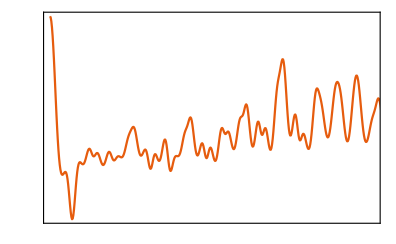

```mathematica
Magnify[fig2, 1]
```

```mathematica
Export[plotsDir<>"/3-trXiXjXiXj.pdf", fig2]
```

../../../plots/plots-thesis/3-trXiXjXiXj.pdf